```mathematica
n=7
b=2
a=-2
h=(b-a)/n
XDT={};YDT={};
For[i=0,i≤n,i++,
xdata[i]=a+i×h;
ydata[i]=N[Exp[-xdata[i]]+0.01*Exp[xdata[i]]*(-1)^(i+2)];
XDT=Append[XDT,xdata[i]];
YDT=Append[YDT,ydata[i]];];
Array[xdata,{n+1,0}];
Array[ydata,{n+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

```mathematica
({{-2}, {-10/7}, {-6/7}, {-2/7}, {2/7}, {6/7}, {10/7}, {2}}) ({{7.390409451763016}, {4.170337373233679}, {2.36066217084043}, {1.3231974245165972}, {0.7647844150497595}, {0.4008086612531134}, {0.2813783752777568}, {0.0614447222473062}})
```

```mathematica
Array[difftab,{n+1,n+1},{0,0}];
For[k=1,k≤n,k++,
For[i=n,i≥n-k,i--,difftab[i,k]=""]];
For[i=0,i≤n,i++,difftab[i,0]=ydata[i]];
For [k=1, k≤n,k++,
For[i=0,i≤n-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata[i+k]-xdata[i])]];
tab1 = Array[difftab,{n+1,n+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

7.39041 | -5.63513 |  2.15967 | -0.57005 |  0.13483 | -0.04602 |  0.02644 | -0.01714
 4.17034 | -3.16693 |  1.18245 | -0.26186 |  0.00334 |  0.04461 | -0.04213 | 
 2.36066 | -1.81556 |  0.73355 | -0.25423 |  0.13081 | -0.09983 |  | 
 1.32320 | -0.97722 |  0.29773 |  0.04476 | -0.15442 |  |  | 
 0.76478 | -0.63696 |  0.37446 | -0.30821 |  |  |  | 
 0.40081 | -0.20900 | -0.15390 |  |  |  |  | 
 0.28138 | -0.38488 |  |  |  |  |  | 
 0.06144 |  |  |  |  |  |  |

```mathematica
pln = difftab[0,0]+difftab[0,1]×(x-xdata[0]);
n=7;lst=List[pln];
For[k=2,k≤n,k++,
pln=lst[[k-1]]+difftab[0,k]×∏_(i=0)^(k-1) (x-xdata[i]);
lst=Append[lst,pln]];
nwtn[x_]:=N[lst[[n]]];
ColumnForm[lst]
```

7.39041-5.63513 (2+x)
7.39041-5.63513 (2+x)+2.15967 (10/7+x) (2+x)
7.39041-5.63513 (2+x)+2.15967 (10/7+x) (2+x)-0.570047 (6/7+x) (10/7+x) (2+x)
7.39041-5.63513 (2+x)+2.15967 (10/7+x) (2+x)-0.570047 (6/7+x) (10/7+x) (2+x)+0.134833 (2/7+x) (6/7+x) (10/7+x) (2+x)
7.39041-5.63513 (2+x)+2.15967 (10/7+x) (2+x)-0.570047 (6/7+x) (10/7+x) (2+x)+0.134833 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0460228 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)
7.39041-5.63513 (2+x)+2.15967 (10/7+x) (2+x)-0.570047 (6/7+x) (10/7+x) (2+x)+0.134833 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0460228 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)+0.0264355 (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)
7.39041-5.63513 (2+x)+2.15967 (10/7+x) (2+x)-0.570047 (6/7+x) (10/7+x) (2+x)+0.134833 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0460228 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)+0.0264355 (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0171412 (-10/7+x) (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)

```mathematica
ColumnForm[Collect[lst,x]]
```

-3.87984-5.63513 x
2.29064+1.76946 x+2.15967 x^2
0.894611-1.53449 x-0.283387 x^2-0.570047 x^3
0.988954-0.981005 x+0.663193 x^2+0.0463309 x^3+0.134833 x^4
0.998155-0.95923 x+0.566585 x^2-0.216656 x^3-0.0624078 x^4-0.0460228 x^5
1.00268-0.953794 x+0.506513 x^2-0.290645 x^3-0.00845779 x^4+0.0446133 x^5+0.0264355 x^6
1.00688-0.951696 x+0.447344 x^2-0.32023 x^3+0.0894919 x^4+0.0935881 x^5-0.00784686 x^6-0.0171412 x^7

```mathematica
data = {{-2,7.390409451763016},{-10/7,4.170337373233679},{-6/7,2.36066217084043},{-2/7,1.3231974245165972},{2/7,0.7647844150497595},{6/7,0.4008086612531134},{10/7,0.2813783752777568},{2,0.0614447222473062}}
inpln:=InterpolatingPolynomial[data,x];
Collect[inpln,x]
```

{{-2,7.39041},{-10/7,4.17034},{-6/7,2.36066},{-2/7,1.3232},{2/7,0.764784},{6/7,0.400809},{10/7,0.281378},{2,0.0614447}}

1.00688-0.951696 x+0.447344 x^2-0.32023 x^3+0.0894919 x^4+0.0935881 x^5-0.00784686 x^6-0.0171412 x^7

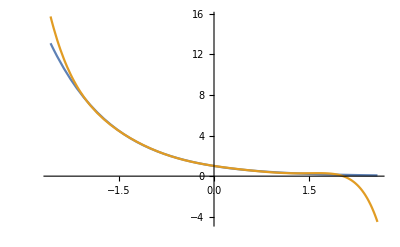

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-h,b+h}]
```

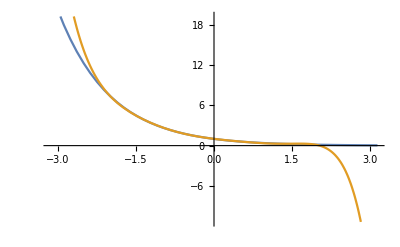

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-2h,b+2h}]
```

```mathematica
Pln={};P[n+1]=0;
For[i=n,i≥0,i--,P[i]=difftab[0,i]+(x-xdata[i])P[i+1];
Pln=Append[Pln,P[i]];]
ColumnForm[Pln]
```

-0.0171412
0.0264355-0.0171412 (-10/7+x)
-0.0460228+(0.0264355-0.0171412 (-10/7+x)) (-6/7+x)
0.134833+(-0.0460228+(0.0264355-0.0171412 (-10/7+x)) (-6/7+x)) (-2/7+x)
-0.570047+(0.134833+(-0.0460228+(0.0264355-0.0171412 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x)
2.15967+(6/7+x) (-0.570047+(0.134833+(-0.0460228+(0.0264355-0.0171412 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))
-5.63513+(10/7+x) (2.15967+(6/7+x) (-0.570047+(0.134833+(-0.0460228+(0.0264355-0.0171412 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x)))
7.39041+(2+x) (-5.63513+(10/7+x) (2.15967+(6/7+x) (-0.570047+(0.134833+(-0.0460228+(0.0264355-0.0171412 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))))

```mathematica
P[0]
```

7.39041+(2+x) (-5.63513+(10/7+x) (2.15967+(6/7+x) (-0.570047+(0.134833+(-0.0460228+(0.0264355-0.0171412 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))))

```mathematica
nwtn[x_]:=P[0];
m=70
XDAT={};YDAT={};nwtnDAT={};MR={};
For[i=0,i≤m,i++,
xdatas[i]=a+i×h/10;
ydatas[i]=N[Exp[-xdatas[i]]];
x=xdatas[i];
nwtndatas[i]=nwtn[i];
mr[i]=Abs[ydatas[i]-nwtndatas[i]];
XDAT=Append[XDAT,xdatas[i]];
YDAT=Append[YDAT, ydatas[i]];
nwtnDAT=Append[nwtnDAT,nwtndatas[i]];
MR=Append[MR,mr[i]];];
MatrixForm[N[XDAT]]MatrixForm[N[YDAT]]MatrixForm[N[nwtnDAT]]MatrixForm[MR]
```

70

(-2.
-1.94286
-1.88571
-1.82857
-1.77143
-1.71429
-1.65714
-1.6
-1.54286
-1.48571
-1.42857
-1.37143
-1.31429
-1.25714
-1.2
-1.14286
-1.08571
-1.02857
-0.971429
-0.914286
-0.857143
-0.8
-0.742857
-0.685714
-0.628571
-0.571429
-0.514286
-0.457143
-0.4
-0.342857
-0.285714
-0.228571
-0.171429
-0.114286
-0.0571429
0.
0.0571429
0.114286
0.171429
0.228571
0.285714
0.342857
0.4
0.457143
0.514286
0.571429
0.628571
0.685714
0.742857
0.8
0.857143
0.914286
0.971429
1.02857
1.08571
1.14286
1.2
1.25714
1.31429
1.37143
1.42857
1.48571
1.54286
1.6
1.65714
1.71429
1.77143
1.82857
1.88571
1.94286
2.) (0.00135335
0.0322566
0.0509454
0.0585305
0.0581794
0.0524831
0.0435247
0.0329435
0.0219933
0.011597
0.00239651
0.005202
0.0109864
0.0149012
0.0170138
0.0174847
0.0165403
0.0144504
0.0115071
0.00800855
0.00424373
0.000481138
0.00304067
0.00612009
0.00859734
0.0103574
0.011331
0.0114944
0.0108671
0.00950873
0.00751477
0.005011
0.0021475
0.000908116
0.00397789
0.00688096
0.00944117
0.0114946
0.0128967
0.0135293
0.0133071
0.0121828
0.010152
0.00725679
0.00358809
0.000713591
0.00545876
0.0104114
0.0152935
0.0197912
0.0235642
0.0262562
0.0275095
0.0269811
0.0243625
0.0194026
0.0119333
0.00189938
0.0106084
0.0253164
0.0417273
0.0590748
0.076274
0.0918678
0.103968
0.110193
0.107596
0.0925961
0.0608952
0.00739571
0.0738906) (7.38906
6.97866
6.59106
6.22499
5.87925
5.55271
5.24431
4.95303
4.67794
4.41812
4.17273
3.94098
3.72209
3.51536
3.32012
3.13571
2.96155
2.79707
2.64172
2.49499
2.35642
2.22554
2.10193
1.98519
1.87493
1.77079
1.67244
1.57955
1.49182
1.40897
1.33071
1.2568
1.187
1.12107
1.05881
1.
0.944459
0.892003
0.84246
0.795669
0.751477
0.70974
0.67032
0.63309
0.597928
0.564718
0.533353
0.50373
0.475753
0.449329
0.424373
0.400803
0.378542
0.357517
0.337661
0.318907
0.301194
0.284466
0.268666
0.253744
0.239651
0.226341
0.213769
0.201897
0.190683
0.180092
0.17009
0.160643
0.151721
0.143294
0.135335) (7.39041
6.9464
6.54012
6.16646
5.82107
5.50022
5.20078
4.92009
4.65594
4.40652
4.17034
3.94618
3.73308
3.53026
3.33713
3.1532
2.97809
2.81152
2.65322
2.503
2.36066
2.22602
2.09889
1.97907
1.86633
1.76044
1.66111
1.56806
1.48096
1.39946
1.3232
1.25179
1.18485
1.12198
1.06278
1.00688
0.9539
0.903498
0.855357
0.809199
0.764784
0.721922
0.680472
0.640347
0.601516
0.564005
0.527894
0.493319
0.460459
0.429538
0.400809
0.374547
0.351032
0.330536
0.313298
0.299504
0.289261
0.282566
0.279275
0.279061
0.281378
0.285415
0.290043
0.293764
0.294651
0.290285
0.277686
0.253239
0.212616
0.15069
0.0614447)

```mathematica
0.11019284502640192
```

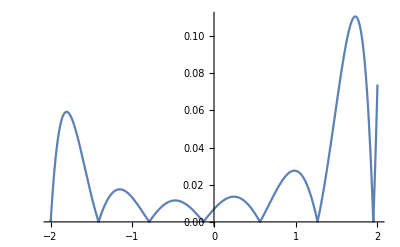

```mathematica
Plot[Abs[Exp[-x]-nwtn[x]],{x,-2,2}]
```

```mathematica
FindMaximum[{Abs[Exp[-x]-nwtn[x]],-2<x<2},{x}]
```

{0.110499,{2→1.72893}}

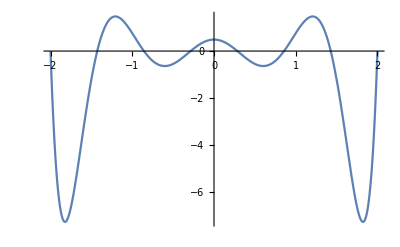

```mathematica
{0.1104992975711907,{2->1.7289278819558571}}
Plot[∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{∏_(i=0)^n (x-xdata[i]),-2≤x≤-1},{x}]
```

```mathematica
{1.4749040152533832,{2->-1.2074687411948342}}
```

```mathematica
ⅇ^2/(8!)×1.4749040152533832
```

```mathematica
0.0002702913816777112
n1=8
b=2
a=-2
h=(b-a)/n1
XDT={};YDT={};
For[i=0,i≤n1,i++,
xdata1[i]=a+i×h;
ydata1[i]=N[Exp[-xdata1[i]]+0.01*Exp[xdata1[i]]*(-1)^(i+2)];
XDT=Append[XDT,xdata1[i]];
YDT=Append[YDT,ydata1[i]];];
Array[xdata1,{n1+1,0}];
Array[ydata1,{n1+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

```mathematica
({{-2}, {-3/2}, {-1}, {-1/2}, {0}, {1/2}, {1}, {3/2}, {2}}) ({{7.390409451763016}, {4.47945776873658}, {2.7219606228707596}, {1.6426559641030019}, {1.01}, {0.5900434470056322}, {0.3950622594560328}, {0.17831326944504916}, {0.20922584422591922}})
```

```mathematica
Array[difftab,{n1+1,n1+1},{0,0}];
For[k=1,k≤n1,k++,
For[i=n1,i≥n1-k,i--,difftab[i,k]=""]];
For[i=0,i≤n1,i++,difftab[i,0]=ydata1[i]];
For [k=1, k≤n1,k++,
For[i=0,i≤n1-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata1[i+k]-xdata1[i])]];
tab1 = Array[difftab,{n+1,n1+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

7.39041 | -5.82190 |  2.30691 | -0.63368 |  0.16248 | -0.06563 |  0.04398 | -0.03171 |  0.02084
 4.47946 | -3.51499 |  1.35638 | -0.30873 | -0.00160 |  0.06630 | -0.06701 |  0.05167 | 
 2.72196 | -2.15861 |  0.89330 | -0.31193 |  0.16415 | -0.13473 |  0.11382 |  | 
 1.64266 | -1.26531 |  0.42540 |  0.01637 | -0.17268 |  0.20672 |  |  | 
 1.01000 | -0.83991 |  0.44995 | -0.32899 |  0.34412 |  |  |  | 
 0.59004 | -0.38996 | -0.04354 |  0.35924 |  |  |  |  | 
 0.39506 | -0.43350 |  0.49532 |  |  |  |  |  | 
 0.17831 |  0.06183 |  |  |  |  |  |  |

```mathematica
(f^(8)(ξ))/8!=0.02084
ξ=0.02084*8!
```

(f^8 ξ)/8≠0.02084

```mathematica
840.2688
```

840.269

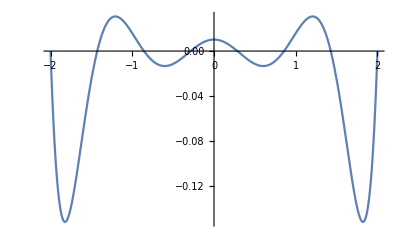

```mathematica
Plot[0.02084*∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{0.02084*∏_(i=0)^n (x-xdata[i]),-2≤x≤2},{x}]
```

```mathematica
{0.03073699967782759,{2->1.20746839904317}}
```